#### Todo : Calculate attraction force between two components before and after firing Calculate magnetic torque that aligns the robots Make demonstration for Gauss Gun we can vary {ballRadius, inertseparatordistance, nextStageSeparation, separatorCoefficientRestitution, numStages] this might be a cool demonstration. Start by drawing them interactively. compute the necessary work to insert a porcupine needle 1 cm: 18 guage needle 2.75 ±0.70 mJ, BarbedQuill 1.06 ±0.37

Forces Before & After Firing

```mathematica
Assuming[d>0,-(8 Msat^2 π r1^3 r2^3 μ0)/3∫_d^∞ 1/x^4 ⅆx]
```

-(8 Msat^2 π r1^3 r2^3 μ0)/(9 d^3)

```mathematica
(* a = airgap
  s = separation dist
r = radius of beads
(2r)[  s ](2r)   a    (2r)[  s ](2r) 
(2r)[  s ]    a   (2r)(2r)[  s ](2r) 
*)
Clear[Msat,μ0,r,s,a];
AttForceEq[r1_,r2_,y_]:=-(8 Msat^2 π r1^3 r2^3 μ0)/(3 y^4) (*Dipole-dipole maximum force for distance  y *)
(*  before firing:
rrsrr|arrsrr
after firing
rrs|arrrrs   INF    rr *)
ForceBefore[r_,s_,a_]:=
AttForceEq[r,r, r+s+2r+a+r]+
AttForceEq[r,r, r+s+2r+a+2r+s+r]+
AttForceEq[r,r, r+a+r]+
AttForceEq[r,r, r+a+2r+s+r];
ForceAfter[r_,s_,a_]:=
AttForceEq[r,r, r+s+ a+r]+
AttForceEq[r,r, r+s+a+3r](*+
AttForceEq[r,r, r+s+a+4r+s+r]*);
RatioForceAfterandBefore[r_,s_,a_]:=FullSimplify[ForceAfter[r,s,a]/ForceBefore[r,s,a]]
ForceMag[sphereRad_,grad_]:=4/3 π sphereRad^3 Msat grad
```

```mathematica
FullSimplify[RatioForceAfterandBefore[1,s,a]]
```

(1/(2+a+s)^4+1/(4+a+s)^4)/(1/(2+a)^4+2/(4+a+s)^4+1/(6+a+2 s)^4)

```mathematica
N[RatioForceAfterandBefore[r,0,0]]
```

0.934193

```mathematica
ForceBefore[r,s,a]
ForceAfter[r,s,a]
FullSimplify[-2ForceMag[r,0.04]/ForceAfter[r,s,a]]/.{s->4 r,a->5 r,Msat ->1.36 10^6,μ0->4π 10^-7}
```

-(8 Msat^2 π r^6 μ0)/(3 (a+2 r)^4)-(16 Msat^2 π r^6 μ0)/(3 (a+4 r+s)^4)-(8 Msat^2 π r^6 μ0)/(3 (a+6 r+2 s)^4)

-(8 Msat^2 π r^6 μ0)/(3 (a+2 r+s)^4)-(8 Msat^2 π r^6 μ0)/(3 (a+4 r+s)^4)

226.543 r

```mathematica
FullSimplify[Evaluate[-ForceMag[r,0.04]/ForceAfter[r,s,a r]-ForceMag[r,0.04]/ForceAfter[r,s,a r+2r]]/.{s->0r}]/.{ r->0.003,Msat ->1.36 10^6,μ0->4π 10^-7}
```

0.00175539 (4.+a)^4 ((0.01 (2.+a)^4)/(136.+a (144.+a (60.+a (12.+a))))+(0.01 (6.+a)^4)/(776.+a (560.+a (156.+a (20.+a)))))

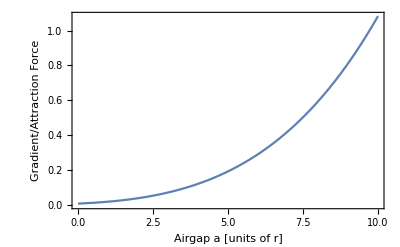

```mathematica
Plot[0.001755385401748846 (0.019999999999999997/(1/(2+a)^4+1/(4+a)^4+1/(6+a)^4)+0.019999999999999997/(1/(4+a)^4+1/(6+a)^4+1/(8+a)^4)),{a,0,10},Frame->{True,True,False,False},
FrameLabel->{"Airgap a [units of r]","Gradient/Attraction Force"}]
```

```mathematica
StringForm["Min and max force ratiso before and after are `` and ``.",N[RatioForceAfterandBefore[r,4 r,4 r]],
N[RatioForceAfterandBefore[r,0 r,0 r]]]
```

Min and max force ratiso before and after are 0.168902 and 0.934193.

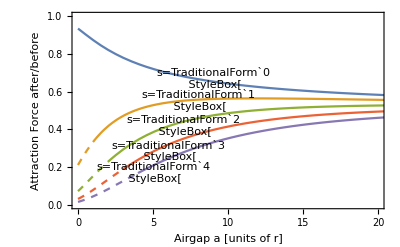

```mathematica
compForceRatio=Plot[Evaluate[Table[RatioForceAfterandBefore[r,s r,a r]*If[a>s,ⅈ,1],{s,0,4}]],{a,0,20},PlotStyle->Dashed,BaseStyle->{FontSize-> 16},
Epilog->{
Table[Text[StringForm["s=r ",s],{9-s,+RatioForceAfterandBefore[ 1,s,8-s
 ]},Background->Directive[Opacity[0.75],White]],{s,0,4}]
},
AxesOrigin->{0,0},PlotRange->{{0,20},{0,1}},
Frame->{True,True,False,False},
FrameLabel->{"Airgap a [units of r]","Attraction Force  after/before"}
];
partForceRatio=Plot[Evaluate[Table[RatioForceAfterandBefore[r,s r,a r]*If[a>s,1,ⅈ],{s,0,4}]],{a,0,25} ];
Show[{compForceRatio,partForceRatio}]
```

TorqueBetween Dipoles.  I need a meaningful comparison.  What is torque compared to the force between the actuators?

```mathematica
BField[r2_,m1_] := μ0/(4π)(3 r2/Norm[r2]((r2/Norm[r2]).m1)-m1)/Norm[r2]^3;(*magnetic field of a dipole located at (0,0)*)
```

```mathematica
Clear[μ0]
BField[{x,0,z},{0,0,mz}]
```

{(3 mz x z μ0)/(4 π (Abs[x]^2+Abs[z]^2)^(5/2)),0,(μ0 (-mz+(3 mz z^2)/(Abs[x]^2+Abs[z]^2)))/(4 π (Abs[x]^2+Abs[z]^2)^(3/2))}

```mathematica
{(3 mz x z μ0)/(4 π (x^2+z^2)^(5/2)),0,(μ0 (-mz+(3 mz z^2)/(x^2+z^2)))/(4 π (x^2+z^2)^(3/2))} (*simplified*)
```

{(3 mz x z μ0)/(4 π (x^2+z^2)^(5/2)),0,((-mz+(3 mz z^2)/(x^2+z^2)) μ0)/(4 π (x^2+z^2)^(3/2))}

```mathematica
BField2D[x_,y_,m1_] :={(μ0 (-m1+(3 x {x/(√(x^2+y^2)),y/(√(x^2+y^2))}.m1)/(√(x^2+y^2))))/(4 π (x^2+y^2)^(3/2)),(μ0 (-m1+(3 y {x/(√(x^2+y^2)),y/(√(x^2+y^2))}.m1)/(√(x^2+y^2))))/(4 π (x^2+y^2)^(3/2))}
```

```mathematica
TorqueMag1on2[s_,θ_,mz1_,mz2_] :={0,0,mz2}×{(3 mz1 x z μ0)/(4 π (x^2+z^2)^(5/2)),0,(μ0 (-mz1+(3 mz1 z^2)/(x^2+z^2)))/(4 π (x^2+z^2)^(3/2))}/.{x->s Cos[θ],z->s Sin[θ]}
```

```mathematica
Assuming [s>0,FullSimplify[TorqueMag1on2[s,θ,mz1,mz2]]]
```

{0,(3 mz1 mz2 μ0 Sin[2 θ])/(8 π s^3),0}

```mathematica
Assuming [s>0,FullSimplify[TorqueMag1on2[s,θ,4/3π r1^3 Ms,4/3π r2^3 Ms]]]
```

{0,(2 Ms^2 π r1^3 r2^3 μ0 Sin[2 θ])/(3 s^3),0}

```mathematica
TorqueForceDipoles[s,r1,r2,θ]/ForceOnDipole[s,r1,r2,θ]
```

(2 Sin[2 θ])/(-1+3 Cos[2 θ])

```mathematica
Clear[Ms,μ0]
TorqueForceDipoles[s_,r1_,r2_,θ_]:=(2 Ms^2 π r1^3 r2^3 μ0 Sin[2 θ])/(3 s^3)/(s/2);
ForceOnDipole[s_,r1_,r2_,θ_]:=(2 Ms^2 π r1^3 r2^3 μ0 (-1+3 Cos[2 θ]))/(3 s^4)(* FullSimplify[((4 Ms^2 π r1^3 r2^3 x (x^2-4 y^2) μ0)/(3 (x^2+y^2)^(7/2))x/√(x^2+y^2)+(4 Ms^2 π r1^3 r2^3 (3 x^2 y-2 y^3) μ0)/(3 (x^2+y^2)^(7/2))y/√(x^2+y^2))/.{x->s Cos[θ],y->s Sin[θ]}] *)
```

```mathematica
Integrate[TorqueForceDipoles[s,r,r,θ],{θ,0,π/2}]/(π/2)
Integrate[ForceOnDipole[s,r,r,θ],{θ,0,π/2}]/(π/2)
```

(8 Ms^2 r^6 μ0)/(3 s^4)

-(2 Ms^2 π r^6 μ0)/(3 s^4)

```mathematica
(8 Ms^2 r^6 μ0)/(3 s^4)/(-(2 Ms^2 π r^6 μ0)/(3 s^4))
```

-4/π

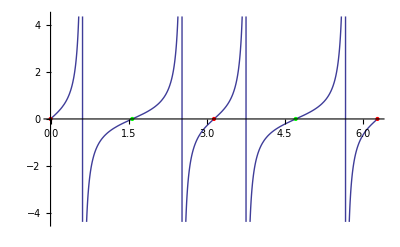

```mathematica
Plot[{(2 Sin[2 θ])/(-1+3 Cos[2 θ])},{θ,0,2π},Ticks->{Table[a,{a,0,2Pi,Pi/4}]},Epilog->{PointSize->Large,
Red,Point[{0,0}],Point[{π,0}],Point[{2π,0}],
Green,Point[{π/2,0}],Point[{(3π)/2,0}]
}]
```

```mathematica
TorqueDipoles[s_,r1_,r2_,θ_]:=(2 Ms^2 π r1^3 r2^3 μ0 Sin[2 θ])/(3 s^3);
```

```mathematica
0.005^3/0.01^3
0.005^3/0.025^3
0.002^3/0.01^3
```

0.125

0.008

0.008

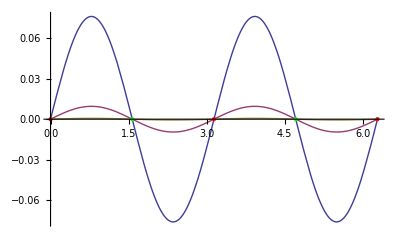

```mathematica
Ms = 1.36 10^6;(*A/m, E52100 Alloy Steel from An MRI-powered and controlled actuator technology for tetherless robotic interventions *)
μ0=4π 10^-7;(*The vacuum permeability μ0 is,by definition,4π×10^-7 V·s/(A·m).*)
Plot[{TorqueDipoles[0.010,0.005,0.005],TorqueDipoles[0.020,0.005,0.005],TorqueDipoles[0.010,0.005,0.001]},{θ,0,2π},Ticks->{Table[a,{a,0,2Pi,Pi/4}]},

PlotRange->All,Epilog->{PointSize->Large,
Red,Point[{0,0}],Point[{π,0}],Point[{2π,0}],
Green,Point[{π/2,0}],Point[{(3π)/2,0}]
}]
```

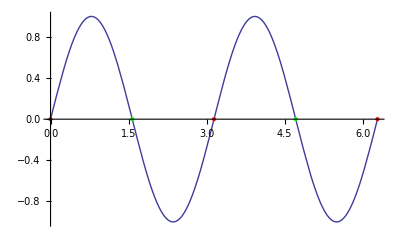

```mathematica
Plot[Sin[2 θ],{θ,0,2π},Ticks->{Table[a,{a,0,2Pi,Pi/4}]},Epilog->{PointSize->Large,
Red,Point[{0,0}],Point[{π,0}],Point[{2π,0}],
Green,Point[{π/2,0}],Point[{(3π)/2,0}]
}]
```

Neodynium Separation Experiment

{344.06,332.01,257.523,229.82,140.88,302.17,308.76,43.99,22.93,7.93}

2048.73/x^4

4753.86/x^4

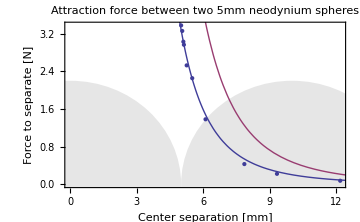

```mathematica
(*TODO: measure greater separations!   This data looks great, and seems to show a fourth-order fit.  Yay! *)
separations={0,0.05,0.25,0.5,1.1,0.125,0.1,2.85,4.32,7.17};(*mm*)
cup = 2.4; (*grams*)
b = 10.6/20; (*grams, weight of bolt*)
masses =cup+{330+22 b, 310+37b, 250+29/3b, 220+14b,130+16b, 295+9b, 300+12b,40+3b,20+1b,5+1b}
sepmassData=Transpose@{5+separations,9.81*masses/1000};
dpl =ListPlot[sepmassData, Frame->{True,True,False,False},FrameLabel->{"Center separation [mm]", "Force to separate [N]"},AxesOrigin->{0,0},
Epilog-> Inset[diagramExp,{9,2.3}],
PlotLabel->"Attraction force between two 5mm neodynium spheres",ImageSize->Medium,
h =2.2;
Prolog->{Thick,Lighter[LightGray],Disk[{0,0},{5,h}],Disk[{10,0},{5,h}]}];
fourthFit = Fit[sepmassData, {1/x^4}, x]
attModel = -AttForceEq[.0025,.0025,x/1000]
Show[dpl,
Plot[{ fourthFit,attModel}, {x, 0, 15}]]
```

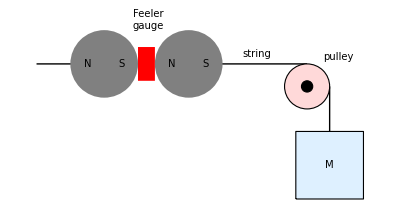

```mathematica
fg = 0.5;
poff = 6;
pdiam = 2/3;
txsz = 10;
diagramExp = Graphics[{Black, Line[{{-2,0},{0,0}}],
 Line[{{3,0},{poff,0}}],
Gray,Disk[{0,0},1],Disk[{2+fg,0},1],
Red,Rectangle[{1,-1/2},{1+fg,1/2}],
Black,Line[{{poff+pdiam,-2/3},{poff+pdiam,-2}}],
EdgeForm[{Black}],LightBlue,
Rectangle[{poff+pdiam-1,-4},{poff+pdiam+1,-2}],
LightRed,
Disk[{poff,-pdiam},pdiam],
Black,
Disk[{poff,-pdiam},1/6],
Text[Style["N",txsz],{-1/2,0}],
Text[Style["S",txsz],{1/2,0}],
Text[Style["N",txsz],{4/2,0}],
Text[Style["S",txsz],{6/2,0}],
Text[Style["Feeler
gauge",txsz],{1.3,1.3}],
Text[Style["pulley",txsz],{poff+pdiam+1/4,.2}],
Text[Style["M",txsz],{poff+pdiam,-3}],
Text[Style["string",txsz],{4.5,.3}],

}]
```

MRI 6mm spheres Separation Experiment:   Neodynium also has a high saturation magnetization (Js ~1.6 T or 16 kG) and typically 1.3 teslas. T=(V*s)/m^2 =N/(A*m)=J/(A*m^2) Coercivity (MA/m) is 0.875–1.99 (Neodymium),  0.493–1.59 Sm-Co

```mathematica
2048.728004493923/4753.859453191376*Msat
```

586107.

```mathematica
AttForceEq[0.0625,0.0625,0.0625*2]
```

-4753.86

```mathematica
Msat = 1.36 10^6;(*A/m, E52100 Alloy Steel from An MRI-powered and controlled actuator technology for tetherless robotic interventions *)
μ0=4π 10^-7;(*The vacuum permeability μ0 is,by definition,4π×10^-7 V·s/(A·m).*)
AttForceEq[r1_,r2_,y_]:=-(8 Msat^2 π r1^3 r2^3 μ0)/(3 y^4) (*Dipole-dipole maximum force for distance y, *)
```

{610.88,246.11,134.52,46.11,151.11,88.76,37.77,882.4}

15318.4/x^4

14194.9/x^4

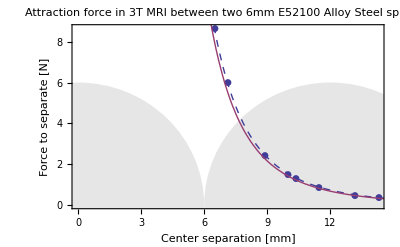

```mathematica
(*TODO: measure greater separations!   This data looks great, and seems to show a fourth-order fit.  Yay! *)
cl = 1.1;
yl = 0.5;
separations={cl,2.85,4.32,7.17,2.85+cl,4.32+cl,7.17+cl,yl};(*mm*)
cup = 2.4; (*grams*)
b = 10.6/20; (*grams, weight of bolt*)
masses =cup+{600+16b,240+7b, 130+4b,40+7b,145+7b,80+12b, 20+29b, 880}
sepmassData=Transpose@{6+separations,9.81*masses/1000};
dpl =ListPlot[sepmassData, Frame->{True,True,False,False},PlotMarkers->Automatic,FrameLabel->{"Center separation [mm]", "Force to separate [N]"},AxesOrigin->{0,0},
h =6;
Epilog-> Inset[diagramExp,{4,2.3}],
Prolog-> {Thick,Lighter[LightGray],Disk[{0,0},{6,h}],Disk[{12,0},{6,h}]},PlotLabel->"Attraction force in 3T MRI
between two 6mm E52100 Alloy Steel spheres"];
fourthFit = Fit[sepmassData, {1/x^4}, x]
attModel = -AttForceEq[.003,.003,x/1000]
Show[dpl,
Plot[{ fourthFit,attModel}, {x, 0, 16},PlotStyle->{Dashed,Automatic}]]
```

What is the work done in Joules?  (this is the potential energy)
s = separation distance
r = ball radius

```mathematica
Clear[r]
```

```mathematica
Clear[μ0,Msat]
AttForceEq[r,r,y]
Assuming[d>0,-∫_d^∞ AttForceEq[r,r,y]ⅆy]
```

-(8 Msat^2 π r^6 μ0)/(3 y^4)

(8 Msat^2 π r^6 μ0)/(9 d^3)

```mathematica
a=(8 Msat^2 π r^6 μ0)/(9 d^3)/.{d->d1};
b=(8 Msat^2 π r^6 μ0)/(9 d^3)/.{d->d2};
FullSimplify[a-b]
a-b
```

(8 (-d1^3+d2^3) Msat^2 π r^6 μ0)/(9 d1^3 d2^3)

(8 Msat^2 π r^6 μ0)/(9 d1^3)-(8 Msat^2 π r^6 μ0)/(9 d2^3)

```mathematica
AttForceEq[r1_,r2_,y_]:=-(8 Msat^2 π r1^3 r2^3 μ0)/(3 y^4)
```

```mathematica
Assuming[r>0,-∫_r^∞ AttForceEq[0.003,0.003,y]ⅆy]
```

(4.73165×10^-9)/r^3

```mathematica
(4.7316494218260634*^-9)/r^3/.r->0.003
```

0.175246

```mathematica
Clear[y,r]
Force[r_,s_]:=Assuming[r>0 && s>r,-∫_r^(s+2r) AttForceEq[r,r,y]ⅆy]
FullSimplify[Force[r,s]]
FullSimplify[Force[r/d,s/d]]
```

r^3 (5.16506×10^12-(5.16506×10^12 r^3)/(2 r+s)^3) μ0

(r^3 (5.16506×10^12-(5.16506×10^12 r^3)/(2 r+s)^3) μ0)/d^3

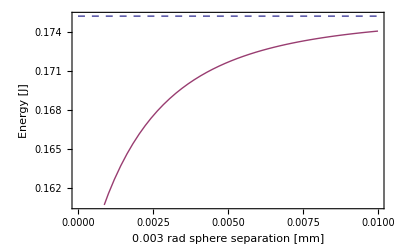

```mathematica
Plot[Evaluate[{6.490602773423956*^6 r^3,6.490602773423956*^6 r^3-(6.490602773423956*^6 r^6)/(2 r+s)^3}/.r->{0.003}],{s,0,0.01},PlotStyle->{ Dashed,Automatic},Frame->{True,True, False, False},FrameLabel->{"0.003 rad sphere separation [mm]","Energy [J]"}]
```

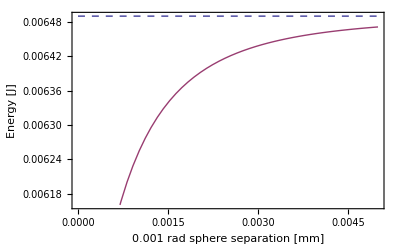

```mathematica
Plot[Evaluate[{6.490602773423956*^6 r^3,6.490602773423956*^6 r^3-(6.490602773423956*^6 r^6)/(2 r+s)^3}/.r->{0.001}],{s,0,0.005},PlotStyle->{ Dashed,Automatic},Frame->{True,True, False, False},FrameLabel->{"0.001 rad sphere separation [mm]","Energy [J]"}]
```

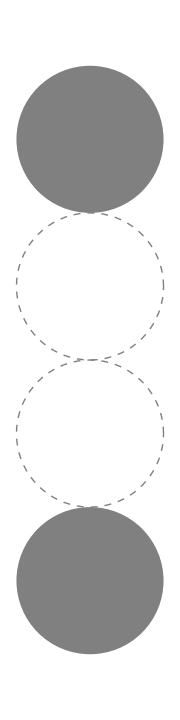

```mathematica
Graphics[{Gray,Dashed,Circle[{0,1},1/2],Circle[{0,2},1/2],Disk[{0,0},1/2],Disk[{0,3},1/2] },ImageSize->Small]
```

## How Does this scale?

How many joules to penetrate?  Notice that power is proportional to the magnetic volume. If the largest volume possible is 2mm, I just need 27x (d=3, d^3)to equal the penetration force of 1 stage with 6mm balls(assuming zero losses..)

### To measure energy on output, I can use salt and measure the distance the sphere flies for a given vertical drop. I can line my shooters up on 80 - 20 aluminum tracks.

### I really need to know how big the lumen of my spine is ...

```mathematica
Force[r_,s_]:=Assuming[r>0 && s>r,-∫_r^(s+2r) AttForceEq[r,r,y]ⅆy]
FullSimplify[Force[r,s]]
FullSimplify[Force[r/d,s/d]]
```

8/9 Msat^2 π r^6 (1/r^3-1/(2 r+s)^3) μ0

(8 Msat^2 π r^6 (1/r^3-1/(2 r+s)^3) μ0)/(9 d^3)

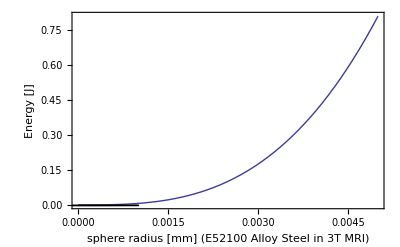

```mathematica
(*plot  how force decreases with ball diameter*)
Plot[6.490602773423956*^6 r^3-(6.490602773423956*^6 r^6)/(2 r+4r)^3,{r,0,0.005},Frame->{True,True, False, False},AxesOrigin->{0,0},
FrameLabel->{"sphere radius [mm] (E52100 Alloy Steel in 3T MRI)","Energy [J]"},
]
```

## Demonstration to optimize Gauss Gun

#### Todo : add coeficient of restitution for steel on steel/steel on titanium, etc Does holding the magnet stationary affect the power? Can I measure distance travelled

```mathematica
BeadSIZEmm =5; (*range 0.5 to 10*) 
Nseg = 3; (*number of segments, 1 to 10*)
Scomp = 20; (*inter-component distance*)
Dcomp = 10; (*intra-component distance*)
Manipulate[
Module[{RightMostEnd,htop,hbot,HolderRad,RightEnd},
RightMostEnd = (Nseg+1)*(4*BeadSIZEmm+Scomp+Dcomp)/2;
htop = 40;
hbot = -40;
HolderRad =4+BeadSIZEmm;
If[ Dcomp ≥Scomp,  Scomp =Dcomp];
Graphics[{
(*{White,Rectangle[{-600,-70},{600,120}]},*)
Text["Before Firing",{0,80}],
(*draw components*)
Table[{
RightEnd = RightMostEnd-(ni-1)*(4*BeadSIZEmm+Scomp+Dcomp);
(*snout*)Cyan,
{Opacity[1/3],Polygon[{{RightEnd-Scomp,htop+HolderRad},{RightEnd,htop+BeadSIZEmm},{RightEnd,htop-BeadSIZEmm},{RightEnd-Scomp,htop-HolderRad}}]},
(*receptor*)Cyan,
{Opacity[1/3],Rectangle[
{RightEnd-(4*BeadSIZEmm+2Scomp+Dcomp),htop+HolderRad},
{RightEnd-(4*BeadSIZEmm+Scomp+Dcomp),htop-HolderRad}]},

(*holder*)Cyan,
{Opacity[2/3],Rectangle[{RightEnd-Scomp -4*BeadSIZEmm-Dcomp,htop-HolderRad },{RightEnd-Scomp,htop+HolderRad}]},

{White,Opacity[1/3],Rectangle[{RightEnd-Scomp -4*BeadSIZEmm-Dcomp,htop-BeadSIZEmm },{RightEnd,htop+BeadSIZEmm}]},
(*seperator*)Lighter[Gray],
Rectangle[{RightEnd-Scomp -2*BeadSIZEmm-Dcomp,htop-BeadSIZEmm},{RightEnd-Scomp -2*BeadSIZEmm,htop+BeadSIZEmm}],
(*beads*)Gray,
Disk[{RightEnd-Scomp-BeadSIZEmm,htop },BeadSIZEmm],
Disk[{RightEnd-Scomp -3*BeadSIZEmm-Dcomp,htop },BeadSIZEmm],

},{ni ,1,Nseg}],

(*firing component*)
RightEnd = RightMostEnd-(Nseg)*(4*BeadSIZEmm+Scomp+Dcomp);
(*snout*)Cyan,
{Opacity[1/3],Polygon[{{RightEnd-Scomp,htop+HolderRad},{RightEnd,htop+BeadSIZEmm},{RightEnd,htop-BeadSIZEmm},{RightEnd-Scomp,htop-HolderRad}}]},
(*holder*)Cyan,
{Opacity[1/3],Rectangle[{RightEnd-2 Scomp -4*BeadSIZEmm,htop-HolderRad },{RightEnd-Scomp,htop+HolderRad}]},
{White,Opacity[1/3],Rectangle[{RightEnd-2Scomp -4*BeadSIZEmm,htop-BeadSIZEmm },{RightEnd,htop+BeadSIZEmm}]},
(*seperator*)Lighter[Gray],
Rectangle[{RightEnd-2 Scomp -2*BeadSIZEmm,htop-BeadSIZEmm },{RightEnd-Scomp -2*BeadSIZEmm,htop+BeadSIZEmm}],
(*beads*)Gray,
Disk[{RightEnd-Scomp-BeadSIZEmm,htop },BeadSIZEmm],
Disk[{RightEnd-2 Scomp -3*BeadSIZEmm,htop },BeadSIZEmm],


Black,Text["Before Firing",{0,0}],
(*draw components*)
{Thick, Red,Arrowheads[BeadSIZEmm/400],Arrow[{{RightMostEnd+1BeadSIZEmm,hbot},{RightMostEnd+6BeadSIZEmm,hbot}}]},
Table[{
RightEnd = RightMostEnd-(ni-1)*(4*BeadSIZEmm+Scomp+Dcomp);
(*snout*)Cyan,
{Opacity[1/3],Polygon[{{RightEnd-Scomp,hbot+HolderRad},{RightEnd,hbot+BeadSIZEmm},{RightEnd,hbot-BeadSIZEmm},{RightEnd-Scomp,hbot-HolderRad}}]},
(*receptor*)Cyan,
{Opacity[1/3],Rectangle[
{RightEnd-(4*BeadSIZEmm+2Scomp+Dcomp),hbot+HolderRad},
{RightEnd-(4*BeadSIZEmm+Scomp+Dcomp),hbot-HolderRad}]},

(*holder*)Cyan,
{Opacity[2/3],Rectangle[{RightEnd-Scomp -4*BeadSIZEmm-Dcomp,hbot-HolderRad },{RightEnd-Scomp,hbot+HolderRad}]},

{White,Opacity[1/3],Rectangle[{RightEnd-Scomp -4*BeadSIZEmm-Dcomp,hbot-BeadSIZEmm },{RightEnd,hbot+BeadSIZEmm}]},
(*seperator*)Lighter[Gray],
Rectangle[{RightEnd-Scomp -2*BeadSIZEmm-Dcomp,hbot-BeadSIZEmm },{RightEnd-Scomp -2*BeadSIZEmm,hbot+BeadSIZEmm}],

(*beads*)Gray,
Disk[{RightEnd-BeadSIZEmm,hbot },BeadSIZEmm],
Disk[{RightEnd-Scomp -3*BeadSIZEmm-Dcomp,hbot },BeadSIZEmm],

},{ni ,1,Nseg}],

(*firing component*)
RightEnd = RightMostEnd-(Nseg)*(4*BeadSIZEmm+Scomp+Dcomp);
(*snout*)Cyan,
{Opacity[1/3],Polygon[{{RightEnd-Scomp,hbot+HolderRad},{RightEnd,hbot+BeadSIZEmm},{RightEnd,hbot-BeadSIZEmm},{RightEnd-Scomp,hbot-HolderRad}}]},
(*holder*)Cyan,
{Opacity[1/3],Rectangle[{RightEnd-2 Scomp -4*BeadSIZEmm,hbot-HolderRad },{RightEnd-Scomp,hbot+HolderRad}]},
{White,Opacity[1/3],Rectangle[{RightEnd-2Scomp -4*BeadSIZEmm,hbot-BeadSIZEmm },{RightEnd,hbot+BeadSIZEmm}]},
(*seperator*)Lighter[Gray],
Rectangle[{RightEnd-2 Scomp -2*BeadSIZEmm,hbot-BeadSIZEmm },{RightEnd-Scomp -2*BeadSIZEmm,hbot+BeadSIZEmm}],
(*beads*)Gray,
Disk[{RightEnd-BeadSIZEmm,hbot },BeadSIZEmm],
Disk[{RightEnd-2 Scomp -3*BeadSIZEmm,hbot },BeadSIZEmm],


},
ImageSize->Large]],{{BeadSIZEmm ,5,"Bead radius (mm)"},0.5,10}, (*range 0.5 to 10*) 
{{Nseg,3,"Segments"},1,10,1}, (*number of segments, 1 to 10*)
{{Scomp , 20,"inter-component distance (mm)"},1,30}, (*inter-component distance  Scomp ≥Dcomp*)
{{Dcomp,  10,"intra-component distance (mm)"},1,30}(*intra-component distance*)]
```

```mathematica
PosAfter[3,1,1,2]
```

{0,6,8,13,15,20,22,∞}

```mathematica
ΔPE[5,0.005,0.010,Sd/1000]
```

```mathematica
Clear[PosBefore,PosAfter,ΔPE]
```

```mathematica
ΔPE[2,0.002,0.008,0.005]
KE = 1/2mv^2
Sqrt[2 Ke/m] = v
```

0.0108076

```mathematica
PEenergy[r_,d_]:= (6.490602773423956*^6 r^6)/d^3
(*Potential energy is only computed for the balls that move, Nseg +1 for the trigger.  The calculation is applied to all 2*Nseg-1 other balls *)
BeadSIZEmm =5; (*range 0.5 to 10*) 
Nseg = 3; (*number of segments, 1 to 10*)
Scomp = 20; (*inter-component distance*)
Dcomp = 10; (*intra-component distance*)
n = 5;
r = 0.003;
Dd = 0.01;
Sd = 0.02;
PosBefore[n_,r_,Dd_,Sd_]:= Accumulate[Flatten[{0,2r+Sd,ConstantArray[{{2r+Sd},{2r+Dd}},n]}]];
PosAfter[n_,r_,Dd_,Sd_]:= Module[{temp},temp=Accumulate[Flatten[{0,2r+2 Sd,ConstantArray[{{2r},{2r+Sd+Dd}},n]}]]; temp⟦-1⟧=∞;temp];
PEBefore[n_,r_,Dd_,Sd_]:=-Total[Table[PEenergy[r,Abs[Drop[PosBefore[n,r,Dd,Sd],{2j}]-PosBefore[n,r,Dd,Sd]⟦2j⟧]],{j,1,n}],2]
PEAfter[n_,r_,Dd_,Sd_]:=-Total[Table[PEenergy[r,Join[PosAfter[n,r,Dd,Sd]⟦1;;2j-1⟧,PosBefore[n,r,Dd,Sd]⟦2j+1;;⟧]-PosAfter[n,r,Dd,Sd]⟦2j⟧],{j,1,n}],2]
ΔPE[n_,r_,Dd_,Sd_] := PEBefore[n,r,Dd,Sd]-PEAfter[n,r,Dd,Sd];
```

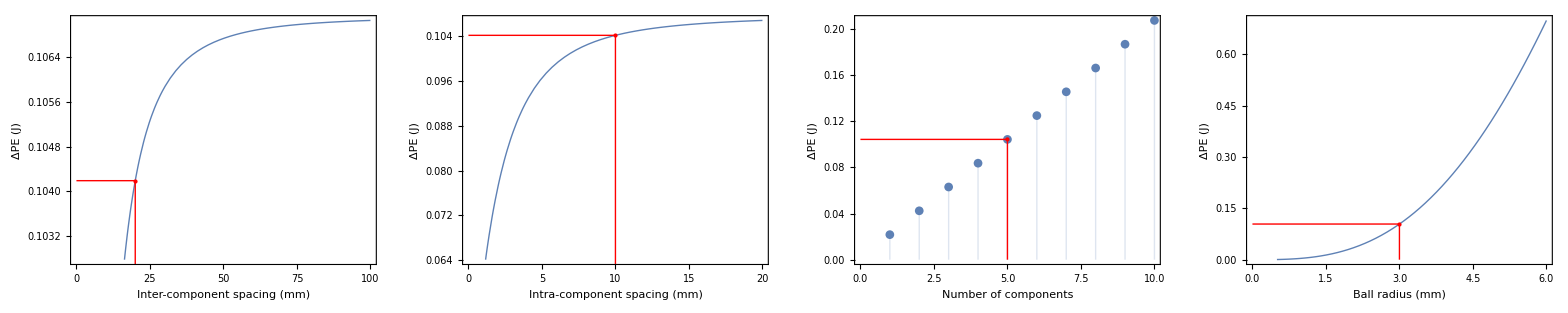

```mathematica
PowerV = ΔPE[n,r,Dd,Sd];
PlotChangeSd =Plot[ΔPE[n,r,Dd,Sd/1000] ,{Sd,1000Dd,100},
Frame->{True,True,False,False},AxesOrigin->{0,Automatic},FrameLabel->{"Inter-component spacing (mm)","ΔPE (J)"},PlotStyle->Thick,BaseStyle->{FontSize-> 24},Epilog->{Red,PointSize[Medium],Point[{1000Sd,PowerV}],Line[{{0,PowerV},{1000Sd,PowerV},{1000Sd,0}}]}];
PlotChangeDd =Plot[ΔPE[n,r,Dd/1000,Sd] ,{Dd,0,1000 Sd},BaseStyle->{FontSize-> 24},
Frame->{True,True,False,False},AxesOrigin->{0,Automatic},FrameLabel->{"Intra-component spacing (mm)","ΔPE (J)"},PlotStyle->Thick,
Epilog->{Red,PointSize[Medium],Point[{1000Dd,PowerV}],Line[{{0,PowerV},{1000Dd,PowerV},{1000Dd,0}}]}];
PlotChangen =DiscretePlot[ΔPE[n,r,Dd,Sd] ,{n,1,10},Filling->Axis,BaseStyle->{FontSize-> 24},
Frame->{True,True,False,False},AxesOrigin->{0,Automatic},FrameLabel->{"Number of components","ΔPE (J)"},PlotStyle->Thick,PlotMarkers->Automatic,Epilog->{Red,PointSize[Medium],Point[{n,PowerV}],Line[{{0,PowerV},{n,PowerV},{n,0}}]}];
PlotChanger =Plot[ΔPE[n,r/1000,Dd,Sd] ,{r,1/2,6},BaseStyle->{FontSize-> 24},
Frame->{True,True,False,False},AxesOrigin->{0,Automatic},FrameLabel->{"Ball radius (mm)","ΔPE (J)"},PlotStyle->Thick,Epilog->{Red,PointSize[Medium],Point[{1000r,PowerV}],Line[{{0,PowerV},{1000r,PowerV},{1000r,0}}]}];
Grid[{{PlotChangeSd,PlotChangeDd,PlotChangen,PlotChanger }}]
```

```mathematica
Manipulate[Module[{PowerV,PlotChangeSd,PlotChangeDd,PlotChangen,PlotChanger},
If[Dd>Sd,Dd = Sd];
PowerV = ΔPE[n,r/1000,Dd/1000,Sd/1000];
PlotChangeSd =Plot[ΔPE[n,r/1000,Dd/1000,Sd/1000] ,{Sd,Dd,30},
Frame->{True,True,False,False},AxesOrigin->{0,Automatic},FrameLabel->{"Inter-component spacing (mm)","ΔPE (J)"},PlotStyle->Thick,Epilog->{Red,PointSize[Medium],Point[{Sd,PowerV}],Line[{{0,PowerV},{Sd,PowerV},{Sd,0}}]}];
PlotChangeDd =Plot[ΔPE[n,r/1000,Dd/1000,Sd/1000] ,{Dd,0,Sd},
Frame->{True,True,False,False},AxesOrigin->{0,Automatic},FrameLabel->{"Intra-component spacing (mm)","ΔPE (J)"},PlotStyle->Thick,
Epilog->{Red,PointSize[Medium],Point[{Dd,PowerV}],Line[{{0,PowerV},{Dd,PowerV},{Dd,0}}]}];
PlotChangen =DiscretePlot[ΔPE[n,r/1000,Dd/1000,Sd/1000] ,{n,1,10},Filling->Axis,
Frame->{True,True,False,False},AxesOrigin->{0,Automatic},FrameLabel->{"Number of components","ΔPE (J)"},PlotStyle->Thick,PlotMarkers->Automatic,Epilog->{Red,PointSize[Medium],Point[{n,PowerV}],Line[{{0,PowerV},{n,PowerV},{n,0}}]}];
PlotChanger =Plot[ΔPE[n,r/1000,Dd/1000,Sd/1000] ,{r,1/2,6},
Frame->{True,True,False,False},AxesOrigin->{0,Automatic},FrameLabel->{"Ball radius (mm)","ΔPE (J)"},PlotStyle->Thick,Epilog->{Red,PointSize[Medium],Point[{r,PowerV}],Line[{{0,PowerV},{r,PowerV},{r,0}}]}];
Grid[{{PlotChangeSd,PlotChangeDd,PlotChangen,PlotChanger }}]
],
{{r ,5,"Bead radius (mm)"},0.5,5}, (*range 0.5 to 5*) 
{{n,3,"Segments"},1,10,1}, (*number of segments, 1 to 10*)
{{Sd , 20,"inter-component distance (mm)"},1,30}, (*inter-component distance  Scomp ≥Dcomp*)
{{Dd,  10,"intra-component distance (mm)"},1,30}(*intra-component distance*)]
```

### Optimize parameters

```mathematica
Clear[r,Dd,Sd]
Maximize[{ΔPE[1,r,Dd,Sd],r>0,Dd≤Sd,Dd≥0,4r+Dd+Sd == 1},{r,Dd,Sd}]
```

{3140.3,{r→0.177909,Dd→2.45273×10^-10,Sd→0.288366}}

```mathematica
Maximize[{ΔPE[1,r,Dd,Sd],r>0,Dd≤Sd,Dd≥0,4r+Dd+Sd ==0.01},{r,Dd,Sd}]
```

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints {Dd - Sd ≤ 0, -0.0025 + 0.25\ Dd + 0.25\ Sd ≤ 0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{5.836×10^-6,{r→0.000193013,Dd→0.00322611,Sd→0.00600184}}

```mathematica
Maximize[{ΔPE[2,r,Dd,Sd],r>0,Dd≤Sd,Dd≥0,4r+Dd+Sd == 1},{r,Dd,Sd}]
```

{3124.27,{r→0.15357,Dd→0.100948,Sd→0.284771}}

```mathematica
Maximize[{ΔPE[4,r,Dd,Sd],r>0,Dd≤Sd,Dd≥0,4r+Dd+Sd == 1},{r,Dd,Sd}]
```

{5385.15,{r→0.146559,Dd→0.15668,Sd→0.257085}}

### Is the ΔPE after all the balls have moved the same as the sum of ΔPE for each moving ball? NO, compare -Total[Table[PEenergy[r,Drop[Abs[PosAfter-PosAfter⟦2j⟧],{2j}]],{j,1,n}],2] -Total[Table[PEenergy[r,Join[PosAfter⟦1;;2j-1⟧,PosBefore⟦2j+1;;⟧]-PosAfter⟦2j⟧],{j,1,n}],2]

```mathematica
PosAfter-PosAfter⟦2⟧
Join[PosAfter⟦1;;2⟧,PosBefore⟦2+1;;⟧]
```

{-0.05,0.,0.01,0.05,0.06,0.1,0.11,0.15}

{0,0.05,0.06,0.08,0.11,0.13,0.16,0.18}

```mathematica
ΔPE[100,r,Dd,Sd]/100
```

0.0206151

```mathematica
ΔPE[1000,r,Dd,Sd]/1000
```

0.0206043

```mathematica
N38, N42, N52, N50, N42SH
```

#### https : // www.kjmagnetics.com/neomaginfo.asp 19. What does the "N rating", or grade, of the neodymium magnets mean?The grade, or "N rating" of the magnet refers to the Maximum Energy Product of the material that the magnet is made from.It refers to the maximum strength that the material can be magnetized to.The grade of neodymium magnets is generally measured in units millions of Gauss Oersted (MGOe).A magnet of grade N42 has a Maximum Energy Product of 42 MGOe.Generally speaking, the higher the grade, the stronger the magnet.

#### Pull force : https : // www.kjmagnetics.com/magnetsummary.asp

Part Number Diameter Grade Pull Force (lb)
S2 1/8 "	N42	0.41
 S3	 3/16" N42 0.91
S4 1/4 "	N42	1.63
 S4B	 1/4 " N42 1.63
S4G 1/4 "	N42	1.63
 S5	 5/16" N42 2.52
S6 3/8 "	N42	3.69
 S6B	 3/8 " N42 3.69
S6G 3/8 "	N42	3.69
 S7	 7/16" N42 4.97
S8 1/2 "	N42	6.53
 SA	 5/8 " N42 10.24
SC 3/4 "	N42	14.74
 SX0	1 " N42 26.37
SX8 1 1/2 "	N42	58.80
 SY0	2 " N42 103.3
Showing 1 to 16 of 16 entries

Experiments on July 24, 2014 with Gauss gun components in Skyra 3 T MRI using 6 mm ball - bearings, firing into 5% Agarose solution

```mathematica
expData =Import[StringJoin[NotebookDirectory[],"../ExperimentGGJuly242014.csv"]]
```

{{Components,Projectile (gauge),Start (mm),End (mm),Distance,Notes},{2,18,1.5,16,14.5,},{2,18,1.5,4,2.5,bead broke from needle tip},{2,26,2,17,15,},{2,26,2,14,12,},{2,26,2,17,15,},{2,26,2,13.5,11.5,},{2,26,2,19,17,},{2,20,2,7,5,},{2,20,2,9,7,},{2,20,2,12,10,},{2,20,2,20,18,},{2,20,2,12,10,},{3,20,2,2,0,},{3,20,2,5,3,},{3,20,2,2,0,},{3,20,2,17,15,bead broke from needle tip},{3,20,2,16,14,},{4,20,2,16,14,},{4,20,2,2,0,},{4,20,2,7,5,},{4,20,2,2,0,},{4,20,2,5,3,},{2,18,2,3,1,Wax Paper},{2,20,1,6,5,},{2,20,1,8,7,},{2,20,1,4,3,},{2,20,1,3,2,},{2,20,1,7,6,}}

```mathematica
Mean[exp[[1,;;,2]]]
```

7.07143

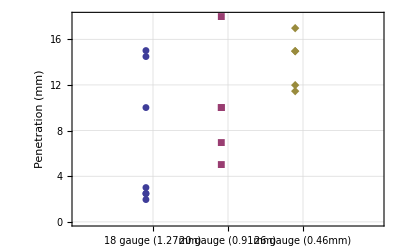

```mathematica
exp = {{{.9,14.5},{.9,2.5},{.9,15},{.9,2},{.9,10},{.9,3},{.9,2.5}},
{{1.9,5},{1.9,7},{1.9,10},{1.9,18},{1.9,10}},
{{2.9,15},{2.9,12},{2.9,15},{2.9,11.5},{2.9,17}}
(*{{2,0},{2,3},{2,0},{2,15},{2,14}},
{{2,14},{2,0},{2,5},{2,0},{2,3}}*)};
exp2 = {{14.5,2.5,15,2,10,3,2.5},
{5,7,10,18,10},
{15,12,15,11.5,17}};
lp =ListPlot[
exp,Frame->{True,True,False,False},FrameLabel->{None,"Penetration (mm)"},FrameTicks->{{{1,"18 gauge
(1.27mm)"},{2,"20 gauge
(0.91mm)"},{3,"26 gauge
(0.46mm)"}},Automatic},PlotRange->{{0,4},Automatic},GridLines->Automatic,PlotMarkers->Automatic,GridLinesStyle->Directive[Dotted,Lighter[Gray]],
Epilog->{}
]
```

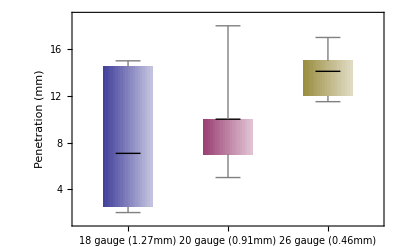

```mathematica
bw =BoxWhiskerChart[exp2,"Mean",ChartStyle->1,ChartElementFunction->"FadingBoxWhisker",FrameLabel->{None,"Penetration (mm)"},ChartLabels->{"18 gauge
(1.27mm)","20 gauge
(0.91mm)","26 gauge
(0.46mm)"}]
```

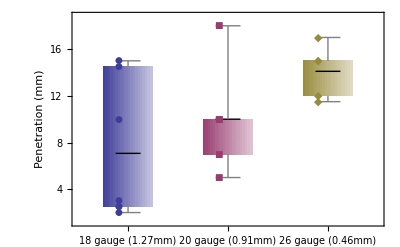

```mathematica
Show[bw,lp]
```

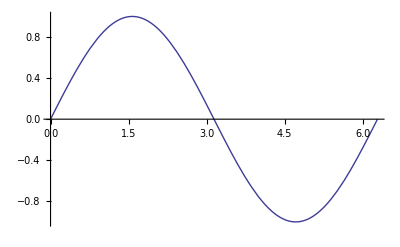

```mathematica
Plot[Sin[x],{x,0,2π}]
```

## MRI magnetic strength of bore magnet

#### I placed a ball - bearing in plastic holder on a 100mm string pinned to the center of a protracter. Distance measured from bore entrance, and measured to the pin-100mm point on the protracter. Angles measured in Degrees. The mass of the ball + plastic is 1.62g. I should have added mass for close up measurements.

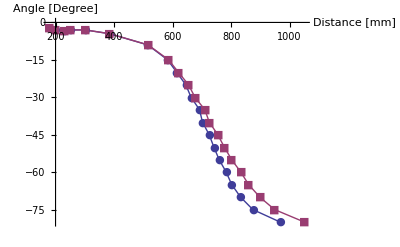

```mathematica
DistanceInmm = {178,200,230,250,301,384,515,583,614,645,663,692,702,725,741,759,783,802,832,874,967};
angleDeg = -{2,3,3.2,3,3,4.5,9,15,20,25,30,35,40,45,50,55,60,65,70,75,80};
DistanceAdjusted = DistanceInmm+100(1-Cos[angleDeg/180*π]);

ListLinePlot[{Transpose[{DistanceInmm,angleDeg}],Transpose[{DistanceAdjusted,angleDeg}]},
PlotMarkers->{Automatic,Small},AxesLabel->{"Distance [mm]","Angle [Degree]"}]
ballAndPlastic = 0.00162; (*kg*)
Fmag = -ballAndPlastic*9.81/Tan[angleDeg π/180];
```

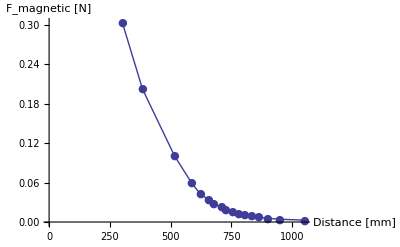

```mathematica
MRIforceBoreData=Transpose[{DistanceAdjusted⟦5;;⟧,Fmag⟦5;;⟧}];
MRIforceBorePlot =ListLinePlot[MRIforceBoreData,
PlotMarkers->{Automatic,Small},AxesLabel->{"Distance [mm]","F_magnetic [N]"},AxesOrigin->{0,0}]
```

{a→1318.57,c→18.6301}

(2.82776×10^9)/x^4

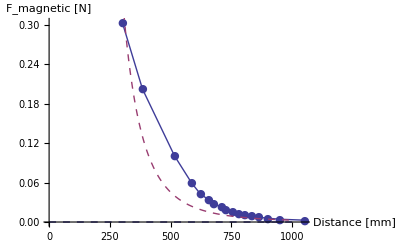

```mathematica
Clear[a]
weirdfit = FindFit[MRIforceBoreData, {c/(x-a)^4},{a,c}, x]
fourthfit = Fit[MRIforceBoreData, {1/x^4}, x]
Show[MRIforceBorePlot,
Plot[{{c/(x-a)^4}/.weirdfit,fourthfit}, {x, 0, 1000},PlotStyle->{Dashed}]]
```

```mathematica
{c/(x-a)^4}/.weirdfit
```

{18.6301/(-1318.57+x)^4}

Magnetic Saturation, page 8 of mse-web
NickelDensity ρ= 8.9 g/cm^3
Atomic weight A_Ni
Avagadro's number N_A
μ_B=magnetidue of Bohr magneton
Bohr magnetons per atom (0.6, given above)
N atoms per cubic meter
M_s=0.6